# DRalgo/DRalgo

DRalgo constructs an effective, dimensionally reduced, high-temperature field theory for generic models

## Paclet Manifest

"FrontEnd"

"logo.eps"FrontEndlogo.eps

"logo.png"FrontEndlogo.png

"logo.svg"FrontEndlogo.svg

"Kernel"

"Debye.m"KernelDebye.m

"DRalgo.m"KernelDRalgo.m

"EffPot.m"KernelEffPot.m

"HardToSoft.m"KernelHardToSoft.m

"HEFT.m"KernelHEFT.m

"ModelCreation.m"KernelModelCreation.m

"SoftToUS.m"KernelSoftToUS.m

"PacletInfo.m"PacletInfo.m

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

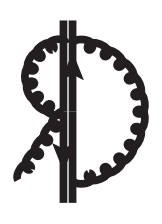

### Basic Description

DRalgo is an algorithmic implementation that constructs an effective, dimensionally reduced, high-temperature field theory for generic models

### Details

DRalgo is an algorithmic implementation that constructs an effective, dimensionally reduced, high-temperature field theory for generic models. The corresponding Mathematica package automatically performs the matching to next-to-leading order. Public release of https://arxiv.org/abs/2205.08815.

To create model files, DRalgo uses functions from GroupMath. Since GroupMath is an external package, any use of the model-creation features in DRalgo should be accompanied by a corresponding citation of: R. M. Fonseca, GroupMath: A Mathematica package for group theory calculations, Comput. Phys. Commun. 267 (2021) 108085 [2011.01764]

### Primary Context

DRalgo`DRalgo`

### Main Guide Page

https://github.com/DR-algo/DRalgo/blob/main/README.md

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
DRalgo`$LoadGroupMath=True;
```

```mathematica
Get["DRalgo`DRalgo`"];
```

-Graphics-DRDRDRDRDRDRDRDRDRDRDRDRDRDRD DRalgo DRDRDRDRDRDRDRDRDRDRDRDRDRDRD
Name: | DRalgo/DRalgo
Version: | 1.3.0
Description: | DRalgo constructs an effective, dimensionally reduced, high-temperature field
theory for generic models
WolframVersion: | 13.+
Creator: | Andreas Ekstedthttps://inspirehep.net/authors/1799400Nonehttps://inspirehep.net/authors/1799400HyperlinkActionRecycledHyperlinkActive, Philipp Schichohttps://inspirehep.net/authors/1639147Nonehttps://inspirehep.net/authors/1639147HyperlinkActionRecycledHyperlinkActive, Tuomas V.I. Tenkanenhttps://inspirehep.net/authors/1507627Nonehttps://inspirehep.net/authors/1507627HyperlinkActionRecycledHyperlinkActive
URL: | https://github.com/DR-algo/DRalgo
Reference: | [2205.08815 [hep-ph]](https://arxiv.org/abs/2205.08815)
Model files: | https://github.com/DR-algo/DRalgo/tree/main/examples
DRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRDRD

paclet:GroupMath/tutorial/GroupMathDoc | XXXXXXXXXXXXXXXXXXXXXXXXXXX GroupMath XXXXXXXXXXXXXXXXXXXXXXXXXXVersion: 1.1.3 (19/December/2024)Author: Renato FonsecaReference: Comput. Phys. Commun. 267 (2021), 2011.01764 [hep-th]Website: http://renatofonseca.net/groupmathBuilt-in documentation: paclet:GroupMath/tutorial/GroupMathDocXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXXX

a::shdw: Symbol a appears in multiple contexts {DRalgo`,Global`}; definitions in context DRalgo` may shadow or be shadowed by other definitions.

b::shdw: Symbol b appears in multiple contexts {DRalgo`,Global`}; definitions in context DRalgo` may shadow or be shadowed by other definitions.

h::shdw: Symbol h appears in multiple contexts {DRalgo`,Global`}; definitions in context DRalgo` may shadow or be shadowed by other definitions.

a::shdw: Symbol a appears in multiple contexts {GroupMath`,Global`}; definitions in context GroupMath` may shadow or be shadowed by other definitions.

b::shdw: Symbol b appears in multiple contexts {GroupMath`,Global`}; definitions in context GroupMath` may shadow or be shadowed by other definitions.

Get::noopen: Cannot open or outdated GroupMath` at /Users/schicho/Library/Wolfram/Applications.
Set DRalgo`$InstallGroupMath=True for automatic installation of GroupMath.

$Aborted

DRalgo`a::shdw: Symbol a appears in multiple contexts {DRalgo`,GroupMath`,Global`}; definitions in context DRalgo` may shadow or be shadowed by other definitions.

DRalgo`b::shdw: Symbol b appears in multiple contexts {DRalgo`,GroupMath`,Global`}; definitions in context DRalgo` may shadow or be shadowed by other definitions.

h::shdw: Symbol h appears in multiple contexts {DRalgo`,Global`}; definitions in context DRalgo` may shadow or be shadowed by other definitions.

### Basic Example of the Abelian Higgs Model

#### Model

Using U(1) in the adjoint representation with Dynkin index {0} and representation R= 1.

```mathematica
Group={"U1"};
RepAdjoint={0};
CouplingName={g1};
```

One complex scalar is present in the theory:

```mathematica
Higgs={{Yϕ},"C"};
RepScalar={Higgs};
```

Fermions are implemented as Weyl spinors.
Therefore, to create one Dirac fermion, one left-handed and one right-handed fermion is needed.
In this model, no fermions are present.

```mathematica
RepFermion={};
```

The input for the gauge interactions to DRalgo is then given by

```mathematica
{gvvv,gvff,gvss,λ1,λ3,λ4,μij,μIJ,μIJC,Ysff,YsffC}=AllocateTensors[Group,RepAdjoint,CouplingName,RepFermion3Gen,RepScalar];
```

To build the Lagrangian, first the mass term is added:

```mathematica
InputInv={{1,1},{True,False}}; (*This specifies that we want a ϕ^+ϕ term*)
MassTerm1=CreateInvariant[Group,RepScalar,InputInv]//Simplify//FullSimplify;
VMass=msq*MassTerm1[[1]];(*This is the ϕ^+ϕ term written in component form*)
μij=GradMass[VMass]//Simplify//SparseArray;
```

Second, we add the quartic interaction of the complex scalar:

```mathematica
QuarticTerm1=MassTerm1[[1]]^2; (*Because MassTerm1=ϕ^+ϕ, we can write (ϕ^+ϕ)^2=MassTerm1^2*)
VQuartic=λ*QuarticTerm1;
λ4=GradQuartic[VQuartic];
```

To invoke the model, it needs to be imported:

```mathematica
ImportModelDRalgo[Group,gvvv,gvff,gvss,λ1,λ3,λ4,μij,μIJ,μIJC,Ysff,YsffC,Verbose->False];
```

#### Dimensional reduction from hard to soft scale

Integrate out the hard-scale modes:

```mathematica
PerformDRhard[]
```

After the reduction completes, the effective couplings are given by:

```mathematica
PrintCouplings[]
```

{g13d^2→g1^2 T-(g1^4 Lb T Yϕ^2)/(48 π^2),λ3d→(T (g1^4 (2-3 Lb) Yϕ^4+6 g1^2 Lb Yϕ^2 λ+2 λ (8 π^2-5 Lb λ)))/(16 π^2)}

Internally, a list of constants is used and they can be printed via:

```mathematica
PrintConstants[]
```

{Lb→2 EulerGamma-2 Log[4 π]+Log[μ^2/T^2],Lf→2 EulerGamma+4 Log[2]-2 Log[4 π]+Log[μ^2/T^2]}

Both the leading order (LO) and next-to-leading order (NLO) scalar masses are given by:

```mathematica
PrintScalarMass["LO"]
PrintScalarMass["NLO"]
```

{msq3d→msq+1/12 T^2 (3 g1^2 Yϕ^2+4 λ)}

{msq3d→1/(576 π^2)(12 g1^2 Yϕ^2 (Lb (9 msq-6 T^2 λ)+2 T^2 λ (1+6 EulerGamma-72 Log[Glaisher]))+24 λ (Lb (-6 msq+T^2 λ)-6 T^2 λ (EulerGamma-12 Log[Glaisher]))+g1^4 T^2 Yϕ^4 (-8-108 EulerGamma+69 Lb+1296 Log[Glaisher])+18 Log[μ3/μ] (8 g13d^4 Yϕ^4-16 g13d^2 Yϕ^2 λ3d+16 λ3d^2+λVL[1]^2))}

Similar the Debye masses are given by:

```mathematica
PrintDebyeMass["LO"]
PrintDebyeMass["NLO"]
```

{μsqU1→1/3 g1^2 T^2 Yϕ^2}

{μsqU1→(g1^2 Yϕ^2 (36 msq+7 g1^2 T^2 Yϕ^2-2 EulerGamma g1^2 T^2 Yϕ^2+12 T^2 λ+2 g1^2 T^2 Yϕ^2 Log[4 π T]-2 g1^2 T^2 Yϕ^2 Log[μ]))/(144 π^2)}

Often one needs the explicit tensors of DRalgo which can be accessed via:

```mathematica
PrintTensorDRalgo[];
```

Order of Tensors:
	(1) Scalar Quartic,
	(2) Vector-Scalar Couplings,
	(3) Temporal-Vector Scalar Couplings,
	(4) Temporal-Vector Quartics,
	(5) Temporal-Vector Mass,
	(6) Scalar Mass,
	(7) Scalar Cubics,
	(8) Temporal Vector-Scalar Cubics,
	(9) Tadpoles

For a specific tensor, e.g. for the scalars quartics, we can print it directly:

```mathematica
PrintTensorDRalgo[1]//MatrixForm
```

((λ[1] | 0
0 | λ[1]/3) | (0 | λ[1]/3
λ[1]/3 | 0)
(0 | λ[1]/3
λ[1]/3 | 0) | (λ[1]/3 | 0
0 | λ[1]))

The hard-scale pressure contribution in the high-temperature expansion is obtained by:

```mathematica
PrintPressure["LO"]
```

(2 π^2 T^4)/45

```mathematica
PrintPressure["NLO"]
```

1/288 (-24 msq T^2-T^4 (5 g1^2 Yϕ^2+4 λ))

```mathematica
PrintPressure["NNLO"]
```

-1/(69120 π^2)(2160 Lb msq^2+720 g1^2 msq T^2 Yϕ^2+4320 EulerGamma g1^2 msq T^2 Yϕ^2-3240 g1^2 Lb msq T^2 Yϕ^2+2000 g1^4 T^4 Yϕ^4-40 EulerGamma g1^4 T^4 Yϕ^4-175 g1^4 Lb T^4 Yϕ^4-1440 Lb msq T^2 λ+240 g1^2 T^4 Yϕ^2 λ+1440 EulerGamma g1^2 T^4 Yϕ^2 λ-1080 g1^2 Lb T^4 Yϕ^2 λ+696 T^4 λ^2-480 EulerGamma T^4 λ^2+8040 g1^4 T^4 Yϕ^4 Log[2]+7200 T^4 λ^2 Log[2]-51840 g1^2 msq T^2 Yϕ^2 Log[Glaisher]-52320 g1^4 T^4 Yϕ^4 Log[Glaisher]-34560 g1^2 T^4 Yϕ^2 λ Log[Glaisher]-17280 T^4 λ^2 Log[Glaisher]+4020 g1^4 T^4 Yϕ^4 Log[π]+2160 T^4 λ^2 Log[π]+1440 T^4 λ^2 Log[π T]-720 g1^4 T^4 Yϕ^4 Log[4 π T]+1440 g1^2 T^4 Yϕ^2 λ Log[4 π T]-2400 T^4 λ^2 Log[4 π T]-4020 g1^4 T^4 Yϕ^4 Log[μ/T]-2160 T^4 λ^2 Log[μ/T]+360 g1^4 T^4 Yϕ^4 Log[μ^2]-720 g1^2 T^4 Yϕ^2 λ Log[μ^2]+480 T^4 λ^2 Log[μ^2]+132000 g1^4 T^4 Yϕ^4 Zeta'[-3]+86400 T^4 λ^2 Zeta'[-3])

Finally, the beta functions of the model are:

```mathematica
BetaFunctions4D[]
```

{g1^2→(g1^4 Yϕ^2)/(24 π^2),λ→(3 g1^4 Yϕ^4-6 g1^2 Yϕ^2 λ+10 λ^2)/(8 π^2),msq→-(msq (3 g1^2 Yϕ^2-4 λ))/(8 π^2)}

#### Dimensional reduction from hard to ''ultrasoft'' scale

Integrate out the soft-scale modes:

```mathematica
PerformDRsoft[{}];
```

After the reduction completes, the effective couplings are given by:

```mathematica
PrintCouplingsUS[]
```

{λ3dUS→λ3d-λVL[1]^2/(32 π √μsqU1),g13dUS^2→g13d^2}

Both the leading order (LO) and next-to-leading order (NLO) scalar masses are given by:

```mathematica
PrintScalarMassUS["LO"]
PrintScalarMassUS["NLO"]
```

{msq3dUS→msq3d-(√μsqU1 λVL[1])/(8 π)}

{msq3dUS→(λVL[1] (-2 λVL[1]-4 Log[μ3/(2 √μsqU1)] λVL[1]+λVLL[1]))/(128 π^2)}

The soft-scale pressure contribution in the high-temperature expansion is obtained by:

```mathematica
PrintPressureUS["LO"]
```

μsqU1^(3/2)/(12 π)

```mathematica
PrintPressureUS["NLO"]
```

-(μsqU1 λVLL[1])/(128 π^2)

Finally, the beta functions of the model are:

```mathematica
BetaFunctions3DUS[]
```

{msq3dUS→(g13dUS^4 Yϕ^4-2 g13dUS^2 Yϕ^2 λ3dUS+2 λ3dUS^2)/(4 π^2)}

#### Effective potential directly

First, the theory scale is chosen:

```mathematica
UseUltraSoftTheory[];
```

The theory now has 2 scalar degrees of freedom

Then, a constant background is introduced to the scalars and the potential calculated:

```mathematica
φvev={0,φ}//SparseArray;
DefineVEVS[φvev];
CalculatePotential[]
```

Finally, the different orders of the potential can be computed:

```mathematica
PrintEffectivePotential["LO"]
```

(msq3dUS φ^2)/2+(λ3dUS φ^4)/4

```mathematica
PrintEffectivePotential["NLO"]
```

-((g13dUS^2 Yϕ^2 φ^2)^(3/2))/(6 π)-((msq3dUS+λ3dUS φ^2)^(3/2))/(12 π)-((msq3dUS+3 λ3dUS φ^2)^(3/2))/(12 π)

```mathematica
PrintEffectivePotential["NNLO"]
```

(g13dUS^2 Yϕ^2 √(g13dUS^2 Yϕ^2 φ^2) √(msq3dUS+λ3dUS φ^2))/(16 π^2)+(3 λ3dUS (msq3dUS+λ3dUS φ^2))/(64 π^2)+(g13dUS^2 Yϕ^2 √(g13dUS^2 Yϕ^2 φ^2) √(msq3dUS+3 λ3dUS φ^2))/(16 π^2)+(λ3dUS √(msq3dUS+λ3dUS φ^2) √(msq3dUS+3 λ3dUS φ^2))/(32 π^2)+(3 λ3dUS (msq3dUS+3 λ3dUS φ^2))/(64 π^2)-(3 λ3dUS^2 φ^2 (1/2+Log[μ3US/(3 √(msq3dUS+3 λ3dUS φ^2))]))/(16 π^2)+1/(4 φ^2)((g13dUS^4 Yϕ^4 φ^4)/(8 π^2)-(g13dUS^2 Yϕ^2 φ^2 (-msq3dUS+2 g13dUS^2 Yϕ^2 φ^2-3 λ3dUS φ^2))/(16 π^2)+(g13dUS^2 Yϕ^2 φ^2 √(g13dUS^2 Yϕ^2 φ^2) √(msq3dUS+3 λ3dUS φ^2))/(8 π^2)-((msq3dUS+3 λ3dUS φ^2)^2 (1/2+Log[μ3US/(√(msq3dUS+3 λ3dUS φ^2))]))/(16 π^2)+((-msq3dUS+g13dUS^2 Yϕ^2 φ^2-3 λ3dUS φ^2)^2 (1/2+Log[μ3US/(√(g13dUS^2 Yϕ^2 φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))/(8 π^2)-1/(16 π^2)(7 g13dUS^4 Yϕ^4 φ^4+(-msq3dUS+g13dUS^2 Yϕ^2 φ^2-3 λ3dUS φ^2)^2-2 g13dUS^2 Yϕ^2 φ^2 (msq3dUS+3 λ3dUS φ^2)) (1/2+Log[μ3US/(2 √(g13dUS^2 Yϕ^2 φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))+1/(4 φ^2)(-(√(g13dUS^2 Yϕ^2 φ^2) (g13dUS^2 Yϕ^2 φ^2-2 λ3dUS φ^2) √(msq3dUS+λ3dUS φ^2))/(16 π^2)+(√(msq3dUS+3 λ3dUS φ^2) ((g13dUS^2 Yϕ^2 φ^2 √(msq3dUS+λ3dUS φ^2))/(4 π)-(√(g13dUS^2 Yϕ^2 φ^2) (g13dUS^2 Yϕ^2 φ^2+2 λ3dUS φ^2))/(4 π)))/(4 π)+(λ3dUS^2 φ^4 (1/2+Log[μ3US/(√(msq3dUS+λ3dUS φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))/(4 π^2)-1/(16 π^2)(g13dUS^4 Yϕ^4 φ^4+4 λ3dUS^2 φ^4-2 g13dUS^2 Yϕ^2 φ^2 (2 msq3dUS+4 λ3dUS φ^2)) (1/2+Log[μ3US/(√(g13dUS^2 Yϕ^2 φ^2)+√(msq3dUS+λ3dUS φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))+1/(4 φ^2)(-(√(g13dUS^2 Yϕ^2 φ^2) (g13dUS^2 Yϕ^2 φ^2+2 λ3dUS φ^2) √(msq3dUS+3 λ3dUS φ^2))/(16 π^2)+(√(msq3dUS+λ3dUS φ^2) (-(√(g13dUS^2 Yϕ^2 φ^2) (g13dUS^2 Yϕ^2 φ^2-2 λ3dUS φ^2))/(4 π)+(g13dUS^2 Yϕ^2 φ^2 √(msq3dUS+3 λ3dUS φ^2))/(4 π)))/(4 π)+(λ3dUS^2 φ^4 (1/2+Log[μ3US/(√(msq3dUS+λ3dUS φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))/(4 π^2)-1/(16 π^2)(g13dUS^4 Yϕ^4 φ^4+4 λ3dUS^2 φ^4-2 g13dUS^2 Yϕ^2 φ^2 (2 msq3dUS+4 λ3dUS φ^2)) (1/2+Log[μ3US/(√(g13dUS^2 Yϕ^2 φ^2)+√(msq3dUS+λ3dUS φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))-(λ3dUS^2 φ^2 (1/2+Log[μ3US/(2 √(msq3dUS+λ3dUS φ^2)+√(msq3dUS+3 λ3dUS φ^2))]))/(16 π^2)

#### Effective potential directly using HEFT

In this example, we assume that the vector and temporal degrees of freedom are heavy in comparison to the scalar. We can therefore integrate them out starting from the soft scale:

```mathematica
UseSoftTheory[];
```

The theory now has 3 scalar degrees of freedom

Then, a constant background is introduced to the scalars and the potential calculated:

```mathematica
φvev={0,φ,0}//SparseArray;
DefineVEVS[φvev];
CalculatePotential[]
```

Before computing the final potential, we need to indicate which temporal scalars and which vectors are heavy, respectively. The function PrepareHET[{scalar_indices},{vector_indices}] indicates which particles are integrated out:

```mathematica
PrepareHET[{3},{1}]
```

This functions similar to PerformDRsoft[{}], and the indices can be found with the commands

```mathematica
PrintScalarRepPositions[]
PrintGaugeRepPositions[]
```

{1;;2}

{1;;1}

After, calculating the effective potential in the HEFT setup,

```mathematica
CalculatePotentialHET[]
```

finally, the different orders of the potential can be computed :

```mathematica
PrintActionHET["LO"]
```

(msq3d φ^2)/2+(λ3d φ^4)/4-((g13d^2 Yϕ3d^2 φ^2)^(3/2))/(6 π)-((μsqU1+1/2 φ^2 λVL[1])^(3/2))/(12 π)

```mathematica
PrintActionHET["NLO"]
```

-(g13d^4 Yϕ3d^4 φ^2 (1/2+Log[μ3US/(√(g13d^2 Yϕ3d^2 φ^2))]))/(32 π^2)+(-(g13d^4 Yϕ3d^4 φ^4 (1/2+Log[μ3US/(2 √(g13d^2 Yϕ3d^2 φ^2))]))/(2 π^2)+(g13d^4 Yϕ3d^4 φ^4 (1/2+Log[μ3US/(√(g13d^2 Yϕ3d^2 φ^2))]))/(8 π^2))/(4 φ^2)-(φ^2 (1/2+Log[μ3US/(2 √(μsqU1+1/2 φ^2 λVL[1]))]) λVL[1]^2)/(64 π^2)+((μsqU1+1/2 φ^2 λVL[1]) λVLL[1])/(128 π^2)

The U(1) gauge bosons also change the scalar fields' kinetic term, printed below is the Z factor:

```mathematica
PrintScalarKineticHET[]//Normal
```

{{-(√(g13d^2 Yϕ3d^2 φ^2))/(3 π φ^2),0},{0,1/2 (-(11 √(g13d^2 Yϕ3d^2 φ^2))/(24 π φ^2)+(φ^2 λVL[1]^2)/(192 π (μsqU1+1/2 φ^2 λVL[1])^(3/2)))}}

## Source & Additional Information

### Creator

Andreas Ekstedt
Philipp Schicho
Tuomas V.I. Tenkanen

### Source Control Repository

https://github.com/DR-algo/DRalgo

### License

GPL-3.0

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Dimensional reduction

Thermal field theory

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Publication of DRalgo 1.0

DRalgo Example files

### Compatibility

#### Wolfram Language Version

13+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.